## Авторегрессионные модели прогнозирования

### Литература

G. E. P. Box, G. M. Jenkins, G. C. Reinsel, G. M. Ljung. Time Series Analysis: Forecasting and Control, 5th Edition (2015)

## 1. Авторегрессия

Авторегрессия – регрессия для ряда на его собственные значения в прошлом:

y_t=α+ϕ_1 y_(t-1)+ϕ_2 y_(t-2)+...+ϕ_p y_(t-p)+ϵ_t,

где y_t – стационарный ряд, ϵ_t – гауссов белый шум с ненулевым средним и постоянной дисперсией σ_ϵ^2.
Такая модель называется моделью авторегрессии порядка p (AR(p)). В этой модели y_t представляет собой линейную комбинацию p предыдущих значений ряда и шумовой компоненты.

## 2. Скользящее среднее

Будем считать, что будущее значение переменной зависит от среднего ее предыдущих значений. Это приводит к идее модели скользящего среднего:

y_t=α+ϵ_t+θ_1 ϵ_(t-1)+θ_2 ϵ_(t-2)+...+θ_q ϵ_(t-q),

где ϵ_t,ϵ_(t-1),...,ϵ_(t-q) – значения шума в q предыдущих моментах времени, α,θ_1,θ_2,...,θ_q – это параметры модели, которые необходимо оценить. Это модель скользящего среднего порядка q (MA(q)).

```mathematica
ϵ=RandomVariate[NormalDistribution[0,1],100];
ClearAll[MovingAverageAnimation]
MovingAverageAnimation[data_,OptionsPattern[{ImageSize->500,RollingWindowRange->{1,10}}]]:=
DynamicModule[{lplt,maplt,r=OptionValue[RollingWindowRange]},
Manipulate[lplt=ListPlot[data,ImageSize->OptionValue[ImageSize],Frame->True,PlotRange->All,Axes->False];
maplt=ListLinePlot[Join[ConstantArray[Null,k],MovingAverage[data,k]],ImageSize->OptionValue[ImageSize],Frame->True,PlotRange->All,Axes->False,PlotStyle->Red];
If[k==1,lplt,Show[{lplt,maplt}]],
{k,r⟦1⟧,r⟦2⟧,1}]
]
MovingAverageAnimation[ϵ]
```

## 3. Модели класса ARMA

### 3.1. ARMA

Модель ARMA – сумма авторегрессионной модели порядка p (AR(p)) и модели скользящего среднего порядка q (MA(q)):

y_t=α+ϕ_1 y_(t-1)+ϕ_2 y_(t-2)+...+ϕ_p y_(t-p)+ϵ_t+θ_1 ϵ_(t-1)+θ_2 ϵ_(t-2)+...+θ_p ϵ_(t-q).

Теорема Вольда: любой стационарный ряд может быть описан моделью ARMA(p,q) с любой точностью.

Упражнение
 
Для ряда lynx.csv построить модель ARMA(2,2).

```mathematica
data = Normal[Import["C:\\Users\\shiro\\Desktop\\6 семестр\\Методы прогнозирования (черн.)\\3. Авторегрессионные модели\\2. Авторегрессионные модели\\lynx.csv","Data"]];
pl = data[[All,2]][[2;;]]
```

{269,321,585,871,1475,2821,3928,5943,4950,2577,523,98,184,279,409,2285,2685,3409,1824,409,151,45,68,213,546,1033,2129,2536,957,361,377,225,360,731,1638,2725,2871,2119,684,299,236,245,552,1623,3311,6721,4254,687,255,473,358,784,1594,1676,2251,1426,756,299,201,229,469,736,2042,2811,4431,2511,389,73,39,49,59,188,377,1292,4031,3495,587,105,153,387,758,1307,3465,6991,6313,3794,1836,345,382,808,1388,2713,3800,3091,2985,3790,674,81,80,108,229,399,1132,2432,3574,2935,1537,529,485,662,1000,1590,2657,3396}

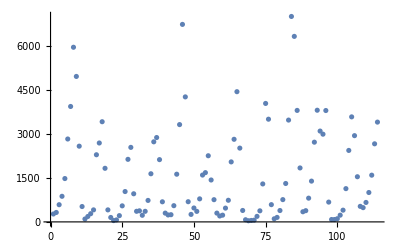

```mathematica
ListPlot[pl]
```

```mathematica
Clear[fun];Clear[α,k,l]
```

```mathematica
fun[y_,t_]:=α+k*y⟦t-1⟧+l*y⟦t-2⟧
```

```mathematica
{pl[[1]]}
```

{269}

```mathematica
result = Minimize[Total@((Join[{pl[[1]]},Table[Thread[fun[pl,i]],{i,3,Length@pl}]]-pl[[2;;]])^2),{α,k,l}]//N
```

{8.69905×10^7,{α→710.106,k→1.15242,l→-0.606229}}

```mathematica
rew = result[[2]][[All,2]]
```

{710.106,1.15242,-0.606229}

```mathematica
res[{a_,k_,l_},y_,t_]:=a+k*y⟦t-1⟧+l*y⟦t-2⟧;
```

```mathematica
ypred = Table[Thread[res[rew,pl,i]],{i,3,Length@pl}];
```

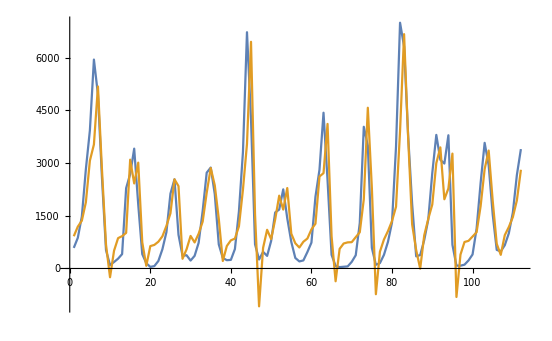

```mathematica
ListLinePlot[{pl[[3;;]],ypred}]
```

```mathematica
residuals = ypred-pl[[3;;]]
```

{331.958,318.673,-115.778,-939.097,-861.098,-2416.35,227.685,234.778,156.065,-347.43,321.985,583.741,511.085,-1272.69,410.444,-989.873,1186.99,336.49,-75.3154,591.174,602.424,548.19,368.348,177.202,-559.443,1.37867,1384.99,-85.4229,168.969,700.72,380.852,257.576,-303.716,-570.38,-13.546,247.737,727.605,-85.2367,404.019,555.815,297.379,-425.283,-1065.15,-3179.13,2194.31,851.046,-1332.08,114.494,742.613,51.9265,-197.425,395.784,-575.763,862.169,232.839,417.854,395.371,531.48,383.158,375.765,-768.033,-193.832,-1719.35,1601.38,528.638,-436.843,519.409,661.795,683.931,560.393,513.994,-261.402,-2060.51,1077.27,1707.11,-837.193,322.254,435.772,305.34,42.0313,-1708.2,-3080.09,353.108,-46.7979,-580.727,180.92,-387.345,133.182,21.6835,-893.165,-804.818,353.612,-1016.43,-1513.77,2594.19,-891.77,314.853,645.195,557.069,509.538,-100.904,-659.237,-747.454,419.515,388.803,173.097,-97.0369,286.335,178.988,-128.795,-720.772,-587.812}

```mathematica
residu[y_,t_]:=α+k*y⟦t-1⟧+l*y⟦t-2⟧
```

```mathematica
result = Minimize[Total@((Join[{residuals[[1]]},Table[Thread[fun[residuals,i]],{i,3,Length@residuals}]]-residuals[[2;;]])^2),{α,k,l}]//N
```

{8.4821×10^7,{α→-4.08743,k→-0.02091,l→-0.149523}}

```mathematica
rew = result[[2]][[All,2]]
```

{-4.08743,-0.02091,-0.149523}

```mathematica
res[{a_,k_,l_},y_,t_]:=a+k*y⟦t-1⟧+l*y⟦t-2⟧;
```

```mathematica
resPred= Table[Thread[res[rew,residuals,i]],{i,3,Length@residuals}];
```

```mathematica
line = ypred[[3;;]]+resPred;
```

```mathematica
ypred;
```

```mathematica
resPred;
```

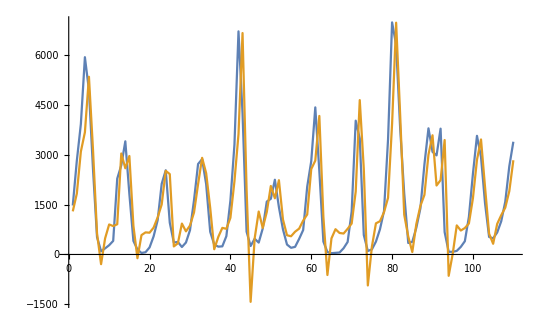

```mathematica
ListLinePlot[{pl[[5;;]],line}]
```

```mathematica
Total@((pl[[5;;]]-line)^2)
```

9.26417×10^7

```mathematica
Total@((pl[[3;;]]-ypred)^2)
```

8.69878×10^7

```mathematica
(Total@Abs[pl[[3;;]]-ypred])/(Length@ypred)
```

636.652

```mathematica
(Total@Abs[pl[[5;;]]-line])/(Length@line)
```

665.331

### 3.2. ARIMA

В основе моделей класса ARIMA лежат идеи о том, что нестационарный ряд можно сделать стационарным при помощи дифференцирования, а любой стационарный ряд может быть описан моделью ARMA(p,q).

Модель авторегресии интегрированного скользящего среднего ARIMA(p,d,q) – это модель ARMA(p,q) для d раз продифференцированного ряда.

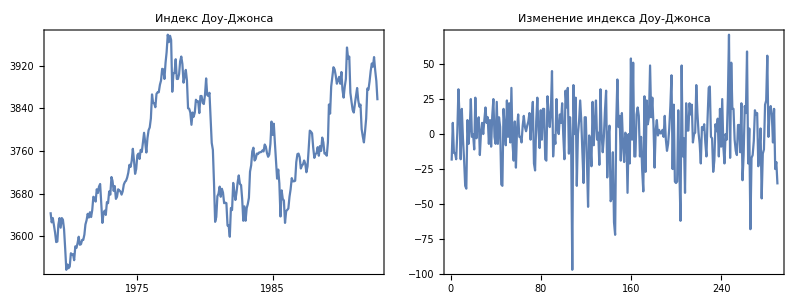

```mathematica
Grid[{{DateListPlot[{DateObject[#⟦1⟧],#⟦2⟧}&/@dowjones⟦2;;-4⟧,PlotLabel->"Индекс Доу-Джонса",ImageSize->400,AspectRatio->3/4],ListLinePlot[Differences@dowjones⟦2;;-4,2⟧,PlotLabel->"Изменение индекса Доу-Джонса",ImageSize->400,Frame->True,Axes->False,AspectRatio->3/4]}},Spacings->2]
```

### 3.3. Критерий Дики-Фуллера

Нестационарный временной ряд описывается модель авторегресии интегрированного скользящего среднего ARIMA(p,d,q), если временной ряд y_t является интегрированным порядка d, d≥1, а  случайный процесс Δ^d y_t является стационарным и описывается моделью ARMA(p,q).

Рассмотрим модель авторегрессии первого порядка AR(1):

y_t=α+ϕ_1 y_(t-1)+ϵ_t.

Временной ряд y_t является стационарным при 0<ϕ_1<1 и нестационарным интегрированным процессом при ϕ_1=1. Во втором случае модель можно записать в следующем виде:

y_t=α+y_(t-1)+ϵ_t.

Такая модель называется моделью случайного блуждания или моделью единичного корня. Таким образом, значение параметра ϕ_1 влияет на тип модели временного ряда:

1) если ϕ_1=1, то временной ряд нестационарный и описывается моделью случайного блуждания;
	2) если ϕ_1<1, то временной ряд стационарный и описывается моделью AR(1).

В первом случае будущие значения рассматриваемого ряда непредсказуемы, а во втором возникает возможность прогнозирования.

Тест Дики-Фуллера проверяет нулевую гипотезу, что ряд является нестационарным и описывается моделью единичного корня при конкурирующей, что ряд является стационарным. Проще говоря, для модели (1) гипотезы принимают вид:

H_0: ϕ_1=1, H_1: ϕ_1<1.

Процедура тестирования включает оценивание параметров модели (1) с помощью МНК и проверку гипотез о значимости коэффициентов модели. Далее рассматриваются пороговые значения t-статистики Дики-Фуллера относительно коэффициента ϕ_1, которые представлены в виде таблиц для различных уровней значимости и различных значений длины ряда.

### 3.4. SARMA

Пусть ряд имеет сезонный период длины S. Возьмем модель ARMA(p,q):

y_t=α+ϕ_1 y_(t-1)+ϕ_2 y_(t-2)+...+ϕ_p y_(t-p)+ϵ_t+θ_1 ϵ_(t-1)+θ_2 ϵ_(t-2)+...+θ_p ϵ_(t-q)

и добавим P авторегрессионных компонент:

+ϕ_S y_(t-S)+ϕ_(2S)y_(t-2S)+...+ϕ_(P S)y_(t-P S)

и Q компонент скользящего среднего:

+θ_S ϵ_(t-S)+θ_(2S)ϵ_(t-2S)+...+θ_(Q S)ϵ_(t-Q S).

Результат – это модель SARMA(p,q)×(P,Q).

### 3.5. SARIMA

Модель SARIMA(p,d,q)×(P,D,Q) – модель SARMA(p,q)×(P,Q) для ряда, к которому d раз было применено обычное дифференцирование и D раз – сезонное. Такую модель часто называют просто ARIMA: первая буква не пишется, но подразумевается, что сезонная компонента тоже может быть.

### 3.6. Прогнозирование

Теперь необходимо разобраться, как на основании настроенной модели ARIMA правильно строить прогноз. Пусть модель построена, определены значения всех неизвестных параметров, получены их оценки α̂; φ̂; θ̂, которые записаны в уравнении:

y_t=α̂+(ϕ̂)_1 y_(t-1)+...+(ϕ̂)_p y_(t-p)+ϵ_t+(θ̂)_1 ϵ_(t-1)+...+(θ̂)_p ϵ_(t-q).

Чтобы построить прогноз на момент времени T+1, нужно в этом уравнении заменить все индексы t на T+1:

(ŷ)_(T+1|T)=α̂+(ϕ̂)_1 y_T+...+(ϕ̂)_p y_(T+1-p)+ϵ_(T+1)+(θ̂)_1 ϵ_T+...+(θ̂)_p ϵ_(t-q).

В этом уравнении присутствует значение ошибки из будущего ϵ_(T+1). Неизвестно, какой будет наблюдаться шум в будущем, однако можно предполагать, что в среднем он будет равен 0. Поэтому значения будущих ошибок можно безболезненно заменить на 0. Фактически из уравнения просто удаляются все члены, которые связаны с ошибками из будущего:

(ŷ)_(T+1|T)=α̂+(ϕ̂)_1 y_T+...+(ϕ̂)_p y_(T+1-p)+(θ̂)_1 ϵ_T+...+(θ̂)_p ϵ_(t-q).

В уравнении также присутствуют ошибки из прошлого. Их необходимо заменить на остатки модели в этих точках, потому они являются самыми лучшими оценками ошибок из имеющихся:

(ŷ)_(T+1|T)=α̂+(ϕ̂)_1 y_T+...+(ϕ̂)_p y_(T+1-p)+(θ̂)_1(ϵ̂)_T+...+(θ̂)_p(ϵ̂)_(T+1-q).

Если прогноз необходимо построить не на одну точку вперёд, а, например, на две, то в формуле появляется значение ряда из будущего y_(T+1):

(ŷ)_(T+2|T)=α̂+(ϕ̂)_1 y_(T+1)+...+(ϕ̂)_p y_(T+2-p)+(θ̂)_1(ϵ̂)_(T+1)+...+(θ̂)_p(ϵ̂)_(T+2-q).

Его необходимо заменить на прогноз (ŷ)_(T+1|T).